```mathematica
x = 400000
x / 150 * 30
```

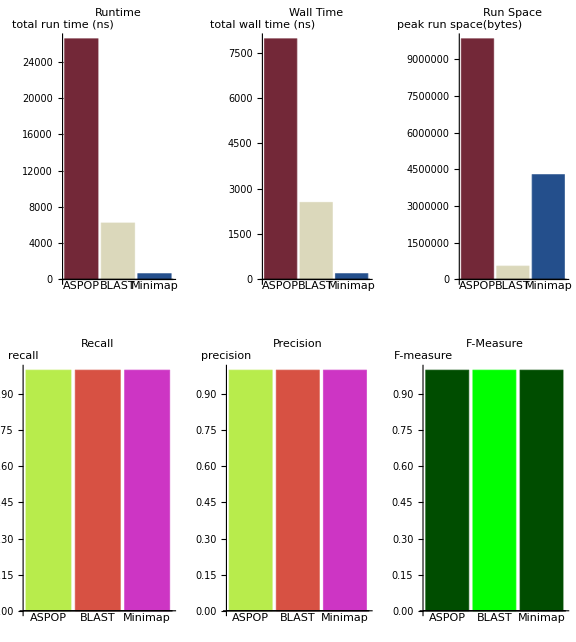

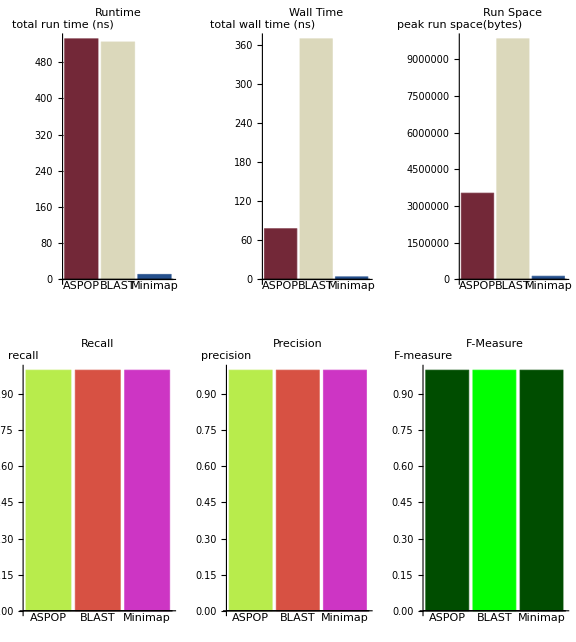

```mathematica
fmeasure[p_, r_]:=2*p*r / (p+r)
plotFour[precs_, recs_, runtimes_, walltimes_,runspaces_, names_]:=
(
fmeasures = Function[x, fmeasure[x[[1]], x[[2]]]] /@ Transpose[{recs, precs}];
cl=Placed[names,Automatic];
ru=BarChart[runtimes, AxesLabel->{"","total run\ntime (ns)"}, ChartLabels->cl, AspectRatio->1.7, ChartStyle->"RedBlueTones", ImageSize->Small, PlotLabel->"Runtime"];
wa=BarChart[walltimes, AxesLabel->{"","total wall\ntime (ns)"}, ChartLabels->cl, AspectRatio->1.7, ChartStyle->"RedBlueTones", ImageSize->Small, PlotLabel->"Wall Time"];
sp=BarChart[runspaces, AxesLabel->{"","peak run\nspace(bytes)"}, ChartLabels->cl, AspectRatio->1.7, ChartStyle->"RedBlueTones", ImageSize->Small, PlotLabel->"Run Space"];

re=BarChart[recs, AxesLabel->{"","recall"}, ChartLabels->cl, AspectRatio->1.7, ChartStyle->"NeonColors", ImageSize->Small, PlotLabel->"Recall"];
pre=BarChart[precs, AxesLabel->{"","precision"}, ChartLabels->cl, AspectRatio->1.7, ChartStyle->"NeonColors", ImageSize->Small, PlotLabel->"Precision"];
fm=BarChart[fmeasures, AxesLabel->{"","F-measure"}, ChartLabels->cl, AspectRatio->1.7, ChartStyle->{Darker[Green, 0.7], Green}, ImageSize->Small, PlotLabel->"F-Measure"];

GraphicsGrid[{{ru,wa, sp}, {re, pre, fm}}, ImageSize->Large]
)

(*ASPOP   |   BLAST   |   Minimap*)
(*VIRAL*)
walltimes={2950*2.7,2508+40, 191};
runtimes={2950*9,6225 ,620+15};
runspaces={7561044*1.3, 544224,4280912};
recalls = {1,1,1};
precisions = {1,1,1};
plotFour[precisions, recalls, runtimes, walltimes,runspaces, {"ASPOP", "BLAST","Minimap"}]

(*HUMAN*)
walltimes={78,370,4};
runtimes={532,525,11};
runspaces={3525196,9832948,130656};
recalls = {1,1,1};
precisions = {1,1,1};
plotFour[precisions, recalls, runtimes, walltimes,runspaces, {"ASPOP", "BLAST","Minimap"}]
```

```mathematica
pr[n_]:=NumberForm[n,Infinity,ExponentFunction->(Null&)];
prec = 0.7045662970996783;
rec = 0.36031372643023246;
abPlusB = 3739999+30936716;
ab = rec*abPlusB;
abPlusA=ab/prec;
a=abPlusA-ab;
{pr[a],pr[ab],pr[abPlusB-ab]}
```

{5239102.910706046,12494496.40200914,22182218.59799086}

```mathematica
(*aspop counts*)
```

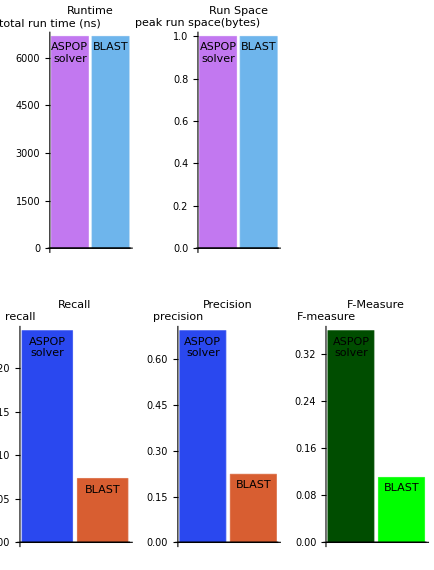

```mathematica
(*Without <80 being cropped*)
bothRecalls = {0.24337610767189075, 0.07335363927728092};
bothPrecisions = {0.6936047567913564, 0.2228631145176301};
plotFour[bothPrecisions, bothRecalls, bothRuntimes, {1,1}, {"ASPOP\nsolver", "BLAST"}]
```

ASPOP x TRUTH
BLAST x TRUTH

ASPOP x BLAST

```mathematica
TRUTH=34676715;
ASPOP=17733599;
BLAST=16659181;
BLASTxTRUTH=3739999;
ASPOPxTRUTH=12494496;
ASPOPxBLAST=?;
uniqueSols= TRUTH
```